```mathematica
δBx[y_]:=(Tanh[10(y+1/2)]-Tanh[10(y-1/2)])-1//FullSimplify
```

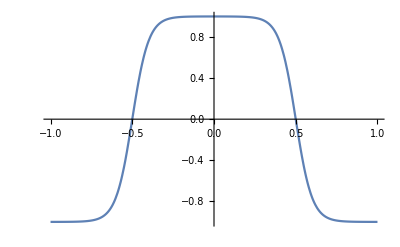

```mathematica
Plot[δBx[y],{y,-1,1}]
```

```mathematica
B[y_,a_]:=1/Sqrt[1+a^2 δBx[y]^2]{a δBx[y],0,-1}
```

```mathematica
Manipulate[
VectorPlot3D[B[y,a],{x,-1,1},{y,-1,1},{z,-1,1},ImageSize->Large,AxesLabel->{"X","Y","Z"}]
,{a,-1/3,1/3}]
```

```mathematica
Manipulate[VectorPlot[B[y,1/2][[{1,3}]],{x,-1,1},{z,-1,1},ImageSize->Large,FrameLabel->{"X","Z"}],{y,-1,1}]
```

```mathematica
FullSimplify[Curl[B[y,a],{x,y,z}],Assumptions->{a>0,y∈Reals}]
```

```mathematica
J[y_,a_]:={-(10 a^2 (Sech[5-10 y]^2-Sech[5+10 y]^2) (-1+Tanh[5-10 y]+Tanh[5+10 y]))/((1+a^2 (-1+Tanh[5-10 y]+Tanh[5+10 y])^2)^(3/2)),0,(10 a (Sech[5-10 y]^2-Sech[5+10 y]^2))/((1+a^2 (-1+Tanh[5-10 y]+Tanh[5+10 y])^2)^(3/2))}
```

```mathematica
VectorPlot3D[J[y,1/2],{x,-1,1},{y,-1,1},{z,-1,1},ImageSize->Large,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
J[y,1/2][[1]]
```

-(5 (Sech[5-10 y]^2-Sech[5+10 y]^2) (-1+Tanh[5-10 y]+Tanh[5+10 y]))/(2 (1+1/4 (-1+Tanh[5-10 y]+Tanh[5+10 y])^2)^(3/2))

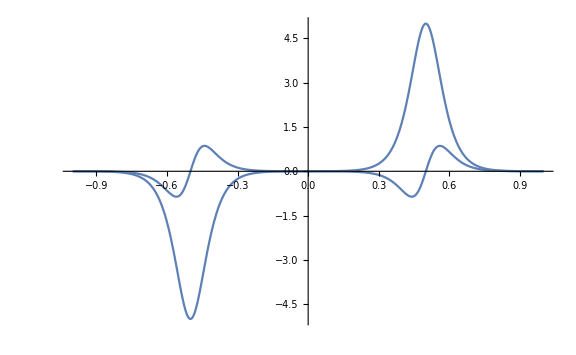

```mathematica
Plot[J[y,1/2][[{1,3}]],{y,-1,1},ImageSize->Large,PlotRange->All]
```

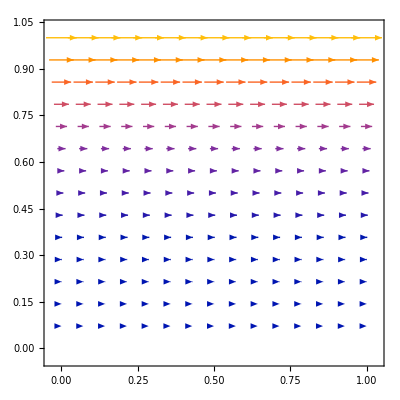

```mathematica
VectorPlot[{z^3,0},{x,0,1},{z,0,1},VectorScale->Automatic]
```